```mathematica
<<Combinatorica`
<<GraphUtilities`
Needs["MATLink`"]
OpenMATLAB[]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

MGet::shdw: Symbol "MGet" appears in multiple contexts {"MATLink`", "Global`"}; definitions in context "MATLink`" may shadow or be shadowed by other definitions.

MEvaluate::shdw: Symbol "MEvaluate" appears in multiple contexts {"MATLink`", "Global`"}; definitions in context "MATLink`" may shadow or be shadowed by other definitions.

```mathematica
Clear[g,AdjacencyMat,Matrix];
START = 1; END = 1000;
Do[MEvaluate["mat = Great_Circles_Problem_3D; close all;"]; AdjacencyMat = IntegerPart[MGet["mat"]];
g[i]=AdjacencyGraph[AdjacencyMat,GraphLayout->"PlanarEmbedding",VertexLabels->Array[#->#&,Length@AdjacencyMat], VertexSize->0.8]; ,{i,START,END}];
Matrix=Table[IsomorphicGraphQ[g[i],g[j]],{i,START,END},{j,START,END}]// PaddedForm
```

General::stop: Further output of MATLink :: errx will be suppressed during this calculation.

```mathematica
Do[mvc=MinimumVertexColoring@ToCombinatoricaGraph[g[i]]; GColored[i]=SetProperty[g[i],System`VertexStyle->Thread[System`VertexList[g[i]]->(ColorData[97]/@mvc)]], {i,{1,2,3,6,9,10,12,15,25,26,41,47,57,78,98,99,163,173,181,227,283,284,296,307,311,331,503,519,576,655,683,839,938,951}}]
```

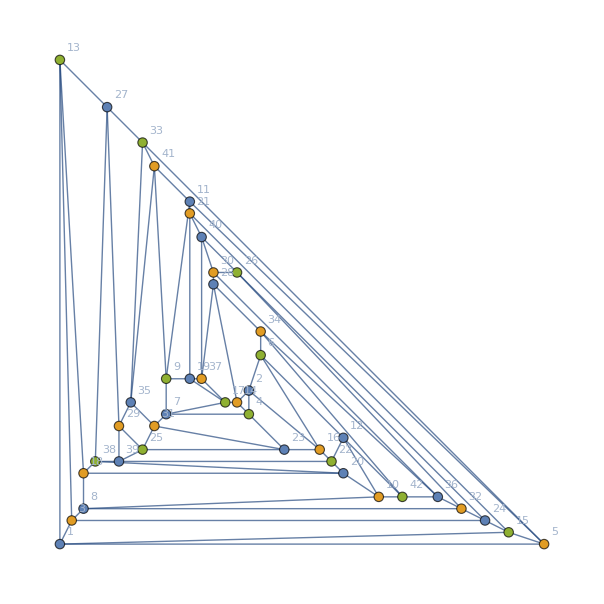
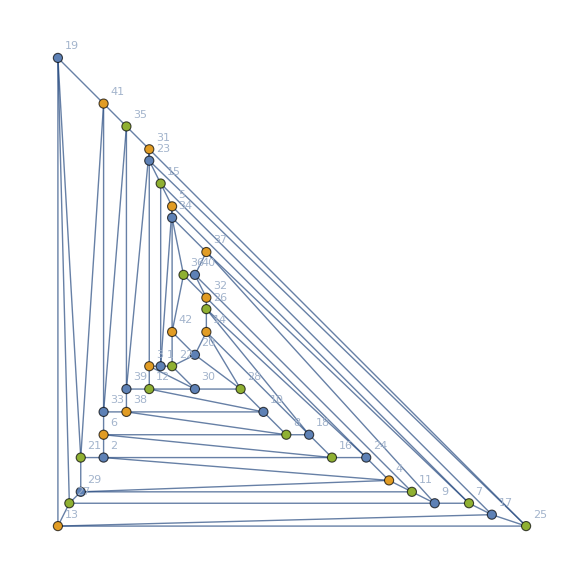
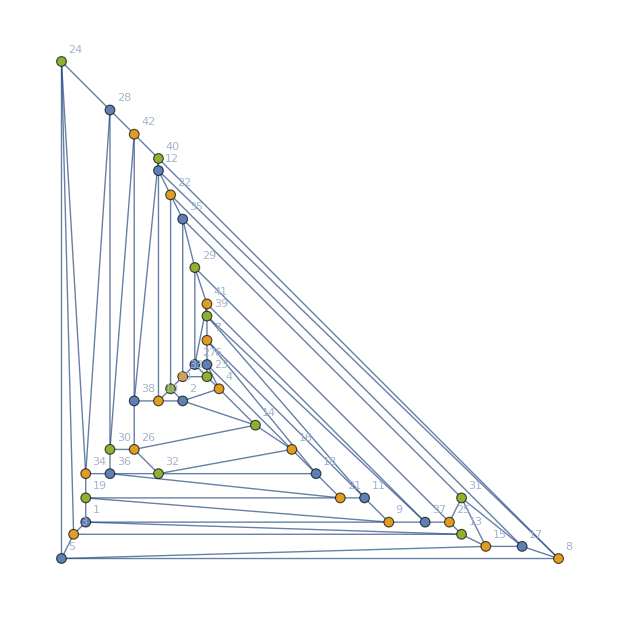
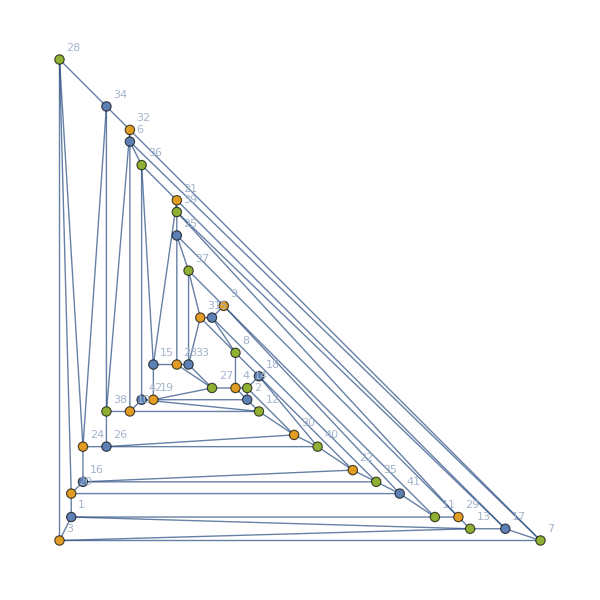
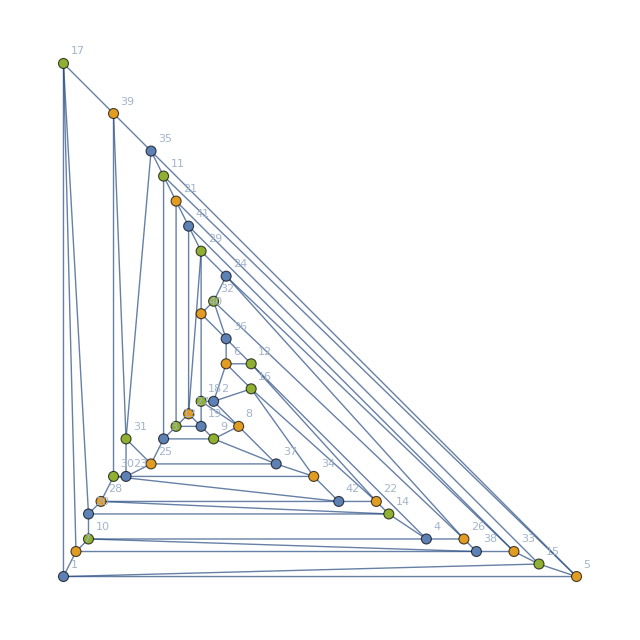
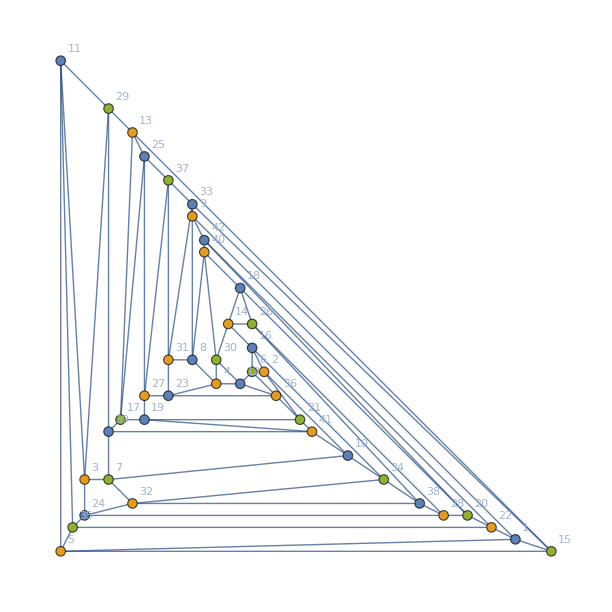
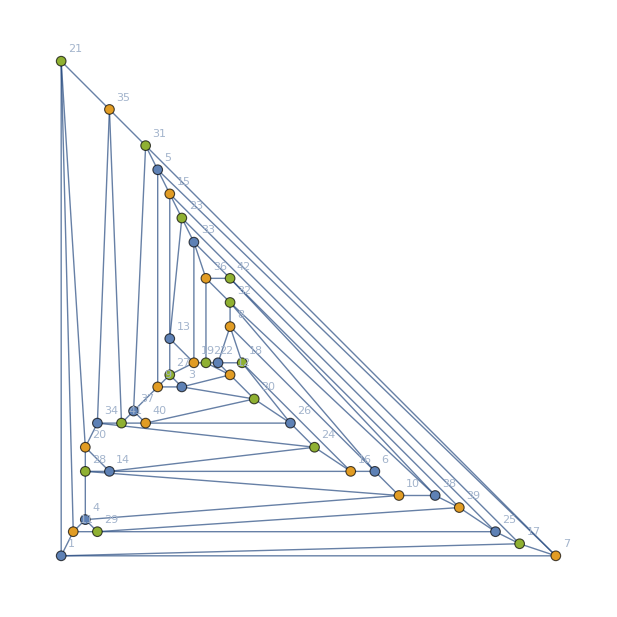
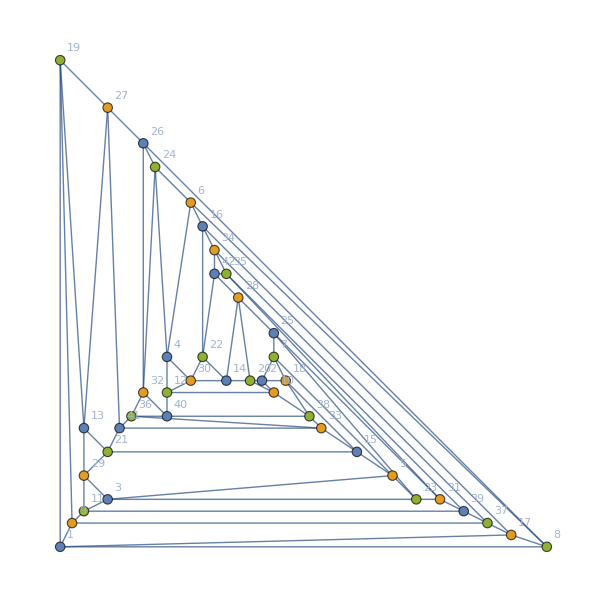

Set::write: Tag Inherited in Inherited["State"] is Protected.

```mathematica
GColored[1]GColored[2]GColored[3]GColored[6]GColored[9]GColored[10]GColored[12]GColored[15]GColored[25]GColored[41]GColored[47]
```